```mathematica
(*Problem 3*)
```

```mathematica
KE= (m/2)*(D[x[t],t]^2+D[y[t],t]^2+D[z[t],t]^2);
```

```mathematica
PE=m*g*z[t];
```

```mathematica
L=KE-PE
```

-g m z[t]+1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)

```mathematica
(*Lagrangian*)
```

```mathematica
L=L/.{x[t]->a*Sin[θ[t]]*Cos[ω*t],y[t]->a*Sin[θ[t]]*Sin[ω*t],z[t]->a*Cos[θ[t]],
x'[t]->D[a*Sin[θ[t]]*Cos[ω*t],t],y'[t]->D[a*Sin[θ[t]]*Sin[ω*t],t],z'[t]->D[a*Cos[θ[t]],t]}//FullSimplify
```

1/2 a m (-2 g Cos[θ[t]]+a ω^2 Sin[θ[t]]^2+a θ'[t]^2)

```mathematica
(*Hamiltonian*)
```

```mathematica
H = D[L,θ'[t]]*θ'[t]-L//FullSimplify
```

1/2 a m (2 g Cos[θ[t]]-a ω^2 Sin[θ[t]]^2+a θ'[t]^2)

```mathematica
1/2 a m (2 g Cos[θ[t]]-a ω^2 Sin[θ[t]]^2+a θ'[t]^2)//TeXForm
```

\frac{1}{2} a m \left(a \theta '(t)^2-a \omega ^2 \sin ^2(\theta
   (t))+2 g \cos (\theta (t))\right)

```mathematica
(*Lagrangian EOM*)
```

```mathematica
FullSimplify[D[D[L,θ'[t]],t]==D[L,θ[t]]]
```

a^2 m θ''[t]==a m (g+a ω^2 Cos[θ[t]]) Sin[θ[t]]

```mathematica
Integrate[Sin[T]*Cos[T],T]
```

-1/2 Cos[T]^2

```mathematica
Series[Sin[t0+e],{e,t0,1}]
```

Sin[2 t0]+Cos[2 t0] (e-t0)+O[e-t0]^2

```mathematica
Series[Sin[T+e],{e,T,2}]
```

Sin[2 T]+Cos[2 T] (e-T)-1/2 Sin[2 T] (e-T)^2+O[e-T]^3

```mathematica
V[T] = (1/2)*(-a*o^2*Sin[T]^2+2*g*Cos[T])
```

1/2 (2 g Cos[T]-a o^2 Sin[T]^2)

```mathematica
D[V[T],{T,2}]//FullSimplify
```

-g Cos[T]-a o^2 Cos[2 T]

```mathematica
D[V[T],{T,2}]//FullSimplify
```

a m (g+4 a o^2 Cos[T]) Sin[T]

```mathematica
D[V[T],{T,3}]//FullSimplify
```

a m (g Cos[T]+4 a o^2 Cos[2 T])

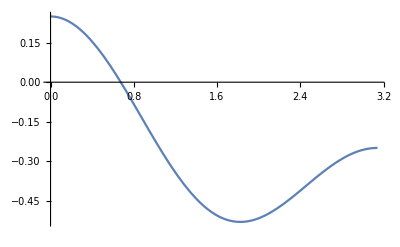

```mathematica
Plot[-Sin[T]^2/2+0.25*Cos[T],{T,0,Pi}]
```